```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Chaozhi\DirectoryWUR\PolyploidProject_AFRI\TestPolyOrigin_4x\RealData\PotatoDiallel\step2-2_run mappoly

```mathematica
dataid="potato_pop3"
```

potato_pop3

```mathematica
map=Import[dataid<>"_genoprob_mappoly_correctid_absphase.csv"][[All,;;3]];
```

```mathematica
Dimensions[map]
```

{4161,3}

```mathematica
{map[[;;10]]//MatrixForm,map[[-10;;]]//MatrixForm}
```

{(marker | chromosome | position
solcap_snp_c2_36608 | 1 | 0.
solcap_snp_c2_36658 | 1 | 0.001
solcap_snp_c1_10930 | 1 | 0.002
PotVar0120130 | 1 | 0.003
PotVar0120070 | 1 | 0.6911
PotVar0120067 | 1 | 0.6921
solcap_snp_c2_36639 | 1 | 1.3755
PotVar0119966 | 1 | 1.3765
solcap_snp_c2_36640 | 1 | 1.3775),(PotVar0052056 | 12 | 142.283
solcap_snp_c2_5710 | 12 | 143.757
solcap_snp_c1_2019 | 12 | 145.247
solcap_snp_c1_2014 | 12 | 145.248
solcap_snp_c1_2004 | 12 | 145.249
solcap_snp_c2_5652 | 12 | 145.25
solcap_snp_c1_1985 | 12 | 147.26
solcap_snp_c2_5463 | 12 | 147.261
solcap_snp_c2_5461 | 12 | 147.262
solcap_snp_c2_5440 | 12 | 147.263)}

```mathematica
chrset=Union[map[[2;;,2]]]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
inmap0=Import["..//step1_data//"<>dataid<>"_dose.csv"];
inmap0[[;;10,;;10]]//MatrixForm
inmap=inmap0[[All,{1,2,3}]];
ls=Select[inmap[[2;;]],(MemberQ[chrset,#[[2]]]&)];
ls=SplitBy[ls,#[[2]]&];
len={#[[1,2]],Length[#],#[[-1,3]]-#[[1,3]]}&/@ls;
len//MatrixForm
Total[len[[All,2]]]
OrderedQ[#[[All,3]]]&/@ls
rule=Thread[#[[All,1]] ->Range[Length[#]]]&/@ls;
```

(Marker | Chrom | Position | VillettaRose | W9914-1R | W15263-56R | W15263-64R | W15263-70R | W15263-33R | W15263-74R
solcap_snp_c2_36608 | 1 | 251132 | 2 | 4 | 3 | 3 | 3 | 2 | 3
solcap_snp_c2_36658 | 1 | 269400 | 2 | 4 | 3 | 3 | 3 | 3 | 4
solcap_snp_c1_10930 | 1 | 309342 | 2 | 4 | 3 | 3 | 3 | 2 | 4
PotVar0120130 | 1 | 353979 | 2 | 4 | 3 | 3 | 3 | 2 | 3
PotVar0120070 | 1 | 433801 | 2 | 4 | 3 | 3 | 3 | 2 | 4
solcap_snp_c2_36629 | 1 | 433801 | 2 | 4 | 3 | 3 | 3 | 2 | 4
PotVar0120067 | 1 | 433987 | 2 | 4 | 3 | 3 | 3 | 2 | 3
solcap_snp_c2_36639 | 1 | 470522 | 2 | 0 | 1 | 1 | 1 | 2 | 1
PotVar0119966 | 1 | 472549 | 2 | 0 | 1 | 1 | 1 | 2 | 1)

(1 | 718 | 88332744
2 | 513 | 46047373
3 | 523 | 61680108
4 | 464 | 71504029
5 | 357 | 51917362
6 | 422 | 59258912
7 | 343 | 56423679
8 | 428 | 56663600
9 | 343 | 61414926
10 | 302 | 59540242
11 | 396 | 45136290
12 | 269 | 60932935)

5078

{True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
ls=SplitBy[map[[2;;]],#[[2]]&];
ls2=Differences[#[[All,3]]]&/@ls;
estlen=Total[#]&/@ls2
ls=Join[len,List/@estlen,2];
Total[ls]
%[[2]]*1.25*10^(-6.)
ls//MatrixForm
```

{197.528,184.731,160.869,156.18,117.08,124.251,117.466,130.907,156.984,112.886,123.648,147.263}

{78,5078,718852200,1729.79}

0.0063475

(1 | 718 | 88332744 | 197.528
2 | 513 | 46047373 | 184.731
3 | 523 | 61680108 | 160.869
4 | 464 | 71504029 | 156.18
5 | 357 | 51917362 | 117.08
6 | 422 | 59258912 | 124.251
7 | 343 | 56423679 | 117.466
8 | 428 | 56663600 | 130.907
9 | 343 | 61414926 | 156.984
10 | 302 | 59540242 | 112.886
11 | 396 | 45136290 | 123.648
12 | 269 | 60932935 | 147.263)

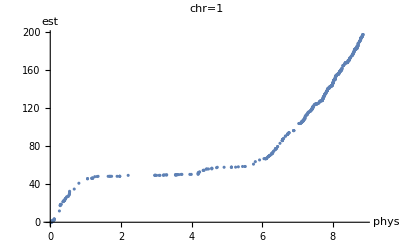
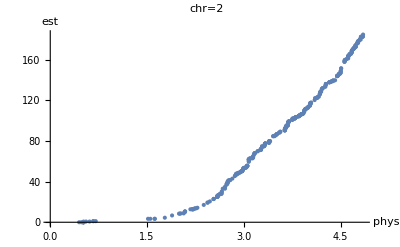
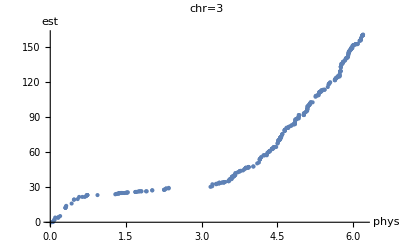
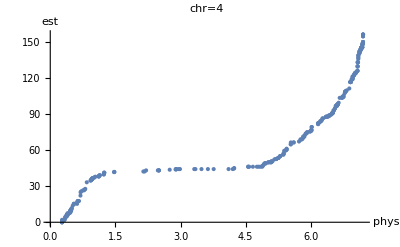
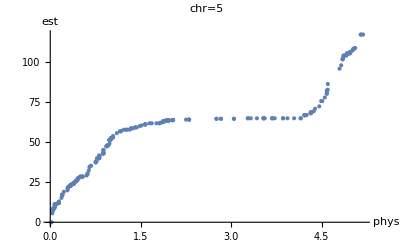
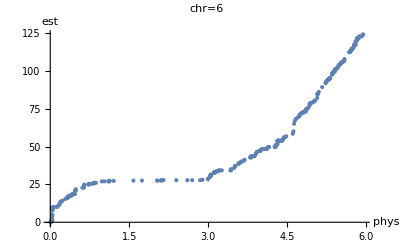
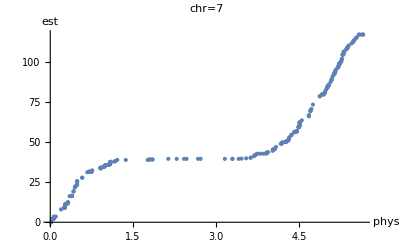
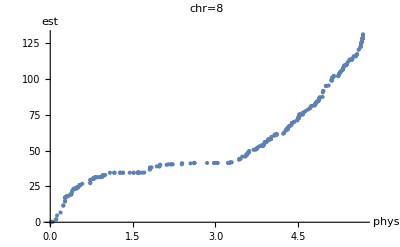

```mathematica
physnprule=Thread[inmap[[2;;,1]]->Range[2,Length[inmap]]];
ls=SplitBy[map[[2;;]],#[[2]]&];
Table[ListPlot[ii=ls[[i]][[All,1]]/.physnprule;Transpose[{inmap[[ii,3]],ls[[i]][[All,3]]}],PlotLabel->"chr="<>ToString[i],AxesLabel->{"phys","est"}],{i,Length[ls]}]
```